## Torsion Pendulum

## Completed and Analyzed in class, March 18, 2025

This is the eleventh notebook for you to complete. It bears strong similarity to our third notebook (Mass on a Spring).

The only significant difference is that a mass on a spring usually has its position measured by its displacement x from equilibrium, whereas a torsion pendulum has its angle θ, measured by its rotation from equilibrium.

### Torque and Angular Acceleration

Torsion is what we might more casually call “twist.” When a material is twisted it generally opposes the twist. If you twist something limp, like a rope candy, it doesn’t oppose the twist very much, and it may even deform so that it stops opposing the twist at all . But if you twist a thin stainless steel wire, it will oppose the twist, and unless you twist it so hard that you damage it, it will oppose the twist until it has returned to its original state. The opposition to the twist is an example of “torque.”

We have used Newton’s Second Law, F=ma, a lot of times. There is a similar formula τ=Iα, that we need to use for the torsion pendulum. Newton’s law is read, “force, F, equals the mass, m, times the acceleration, a.” The new formula involving torque is read, “torque, τ, equals the moment of inertia, I, times angular acceleration, α.” I want to mention and stress that this is not an independent law. In a mechanics course, you would derive this law from Newton’s Second Law.

So we suppose we have a rod with a moment of inertia, I, and it is connected to two fixed walls by two thin stainless wires. The wires oppose the twist. The amount they oppose it is defined by some constant κ and the amount of twist.

Here is the formula:

τ=-κ_Lθ-κ_R θ

We combine this with τ=Iα to get:

α=(-κ_Lθ-κ_R θ)/I

```mathematica
momentOfInertia=0.1;
kappaLeft=0.5;
kappaRight=0.5;
omega0=Sqrt[(kappaLeft+kappaRight)/momentOfInertia];
α[theta_]:=-omega0^2 theta;
```

### Graphics

```mathematica
halfHeight=1;
halfDepth=1;
halfWidth=5;
region={FaceForm[{Blue,Opacity[0.1]}],Cuboid[{-halfWidth,-halfDepth,-halfHeight},{halfWidth,halfDepth,halfHeight}]};
leftWire={Red,Line[{{-halfWidth,0,0},{0,0,0}}]};
rightWire={Green,Line[{{0,0,0},{halfWidth,0,0}}]};
torsionRodGraphic[angle_]:=Graphics3D[{
region,
leftWire,
rightWire,
{Black, Thick,Line[{{0,-halfDepth Cos[angle],halfHeight Sin[angle]},{0,halfDepth Cos[angle],-halfHeight Sin[angle]}}]}
}]
torsionRodGraphic[20°]
```

-Graphics3D-

### Simulation Parameters

```mathematica
tInitial = 0.0;
numberOfPeriods = 10;
period = 2Pi/omega0; 
tFinal = numberOfPeriods period; 
steps =1000 numberOfPeriods;
deltaT = (tFinal - tInitial)/steps;
```

### Initial Angle and Angular Velocity

Let’s let the pendulum be initially held still at 20° and released:

```mathematica
tInitial=0.0;
thetaInitial=20 °;
omegaInitial=0;
initialConditions={tInitial,thetaInitial,omegaInitial};
```

### Second-Order Runge-Kutta — Theory

t^*=t+Δt/2

θ^*=θ(t_i)+ω(t_i)·Δt/2

t_(i+1)=t_i+Δt

ω(t_(i+1))=ω(t_i)+α(θ^*)·Δt

θ(t_(i+1))=θ(t_i)+ (ω(t_i)+ω(t_(i+1)))Δt/2

### Second-Order Runge-Kutta — Implementation

```mathematica
rungeKutta2[cc_]:=(
(* Extract time, angle, and angular velocity from the list *)
curTime=cc[[1]];
curTheta=cc[[2]];
curOmega=cc[[3]];
(* Compute tStar, and thetaStar *)
tStar=curTime + deltaT/2;
thetaStar=curTheta+curOmega deltaT/2;
(* Compute newTime, newTheta, and newOmega *)
newTime=curTime+deltaT;
newOmega=curOmega+α[thetaStar]deltaT;
newTheta=curTheta+(curOmega+newOmega)deltaT/2;
{newTime, newTheta, newOmega}
)
N[rungeKutta2[initialConditions]] (* Test the rungeKutta2 function you just completed. *)
(* The output just below should be {0.00198692,0.349059,-0.00693565} *)
```

{0.00198692,0.349059,-0.00693565}

#### Displaying Oscillation as a Graph

Nest the procedure, transpose the results, and produce a plot of the angle θ as a function of time:

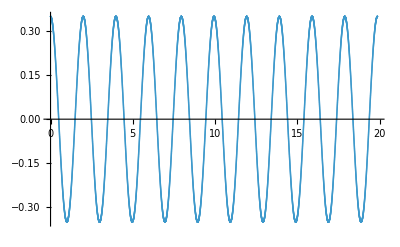

```mathematica
rk2Results=NestList[rungeKutta2,initialConditions, steps];rk2ResultsTransposed=Transpose[rk2Results];
times = rk2ResultsTransposed[[1]];
thetas = rk2ResultsTransposed[[2]];
thetaPlot = ListPlot[Transpose[{times,thetas}]]
```

#### Animating the 3D Graphics

It’s also nice to have an animation, arranged so that the default duration of the animation is the actual duration of the animation:

```mathematica
Animate[torsionRodGraphic[thetas[[step]]],{step, 0, steps, 1}, DefaultDuration->tFinal-tInitial]
```